```mathematica
Integrate[Exp[-I n t],t]
```

(ⅈ ⅇ^(-ⅈ n t))/n

```mathematica
Integrate[Exp[-I n t],{t,0,2π}]
```

-(ⅈ (1-ⅇ^(-2 ⅈ n π)))/n

```mathematica
FullSimplify[ⅇ^(- ⅈ n π),Assumptions->n∈Integers]
```

(-1)^n

```mathematica
g[t_]:=π^2/6-1/2(t-π)^2
```

```mathematica
FullSimplify[Integrate[Exp[-I n t],{t,0,2π}],Assumptions->n ∈Integers]
```

-(2 π)/n^2

```mathematica
Integrate[-1/2 x^2 Exp[-I n (x+π)],{x,-π,π}]
```

-(ⅇ^(-ⅈ n π) (2 n π Cos[n π]+(-2+n^2 π^2) Sin[n π]))/n^3

```mathematica
f[x_]:=I x^2 Exp[-I n x]/n;
h[x_]:=2x Exp[-I n x]/n^2;
```

```mathematica
h[Pi]-h[-Pi]
```

(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2

```mathematica
ExpToTrig[h[Pi]-h[-Pi]]
```

(4 π Cos[n π])/n^2

```mathematica
TeXForm@FullSimplify[ExpToTrig[h[Pi]-h[-Pi]],Assumptions->n∈Integers]
```

\frac{4 \pi  (-1)^n}{n^2}

```mathematica
(f[Pi]-f[-Pi])
```

(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n

```mathematica
ExpToTrig[(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n]
```

(2 π^2 Sin[n π])/n

```mathematica
FullSimplify[(2 π^2 Sin[n π])/n,Assumptions->n∈Integers]
```

0

```mathematica
Simplify[(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n]
```

-(ⅈ ⅇ^(-ⅈ n π) (-1+ⅇ^(2 ⅈ n π)) π^2)/n

```mathematica
-2/n^2 Integrate[E^(-I n x),{x,-Pi,Pi}]
```

-(4 Sin[n π])/n^3

```mathematica
FourierCoefficient[g[t+π],t,n]
```

Piecewise[{{0, n==0}, {(-1)^(1+n)/n^2, True}}]

```mathematica
Integrate[]
```

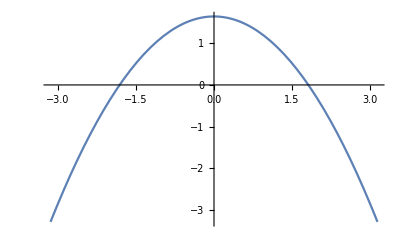

```mathematica
Plot[g[t+π],{t,-π,π}]
```

```mathematica
g[t-π]
```

π^2/6-1/2 (-2 π+t)^2

```mathematica
h[x_]:=2x Exp[-I n x]/n^2;
```

```mathematica
Integrate[x^2 Exp[-I n x],{x,-π,π}]//TrigToExp
```

(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3

```mathematica
Reduce[((2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3)
==h[π]-h[-π]-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3==-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(4 ⅇ^(-ⅈ n π) π)/n^2+(4 ⅇ^(ⅈ n π) π)/n^2]

```mathematica
Integrate[x^2 Exp[-I n x],{x,-π,π}]//TrigToExp
```

(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3

```mathematica
-(2I)/n Integrate[x Exp[-I n x],{x,-Pi,Pi}]//TrigToExp
```

-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2

```mathematica
FullSimplify[Exp[-I n π],Assumptions->n ∈Integers]
```

(-1)^n

```mathematica
j[x_]:=Exp[-I n x]((I x^2)/n+(2x)/n^2-(2i)/n^3)
```

```mathematica
j[π]-j[-π]
```

-ⅇ^(ⅈ n π) (-(2 i)/n^3-(2 π)/n^2+(ⅈ π^2)/n)+ⅇ^(-ⅈ n π) (-(2 i)/n^3+(2 π)/n^2+(ⅈ π^2)/n)

```mathematica
Simplify[j[π]-j[-π],Assumptions->n∈Integers]
```

```mathematica
(4 (-1)^n π)/n^2 G[t_]:=g[t-(Floor[t/(2π)](2π))]
```

```mathematica
E^(I π)
```

-1

```mathematica
FullSimplify[Integrate[(t-π)^2 Exp[-I n t],{t,0,2π}],Assumptions->n∈Integers]
```

(4 π)/n^2

```mathematica
G[t_]:=π^2/6-1/2(t-π)^2;
g[t_]:=G[t-(Floor[t/(2π)](2π))]
```

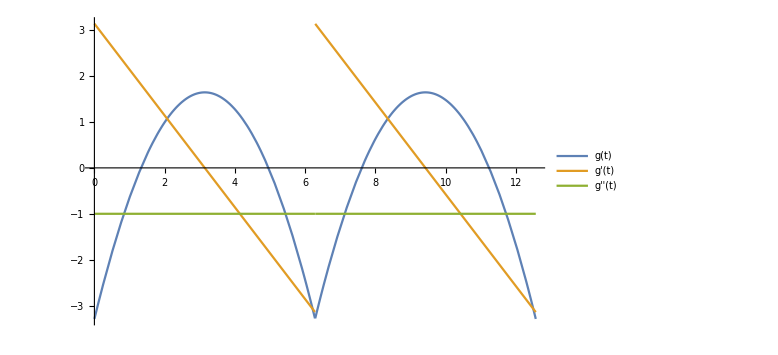

```mathematica
fig=Plot[{g[t],g'[t],g''[t]},{t,0,4π},AxesOrigin->{0,0},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
Export["~/school/FA22/PHYS161a/figs/fourierplot.png",fig]
```

~/school/FA22/PHYS161a/figs/fourierplot.png

```mathematica
Sum
```

Problem 4

```mathematica
El[r_]:=E0 H[a-r]
```

```mathematica
1/r^2 D[r^2 El[r],r]
```

(2 E0 r H[a-r]-E0 r^2 H'[a-r])/r^2

```mathematica
Simplify[(2 E0 r H[a-r]-E0 r^2 H'[a-r])/r^2]
```

(2 E0 H[a-r])/r-E0 H'[a-r]

```mathematica
Integrate[2r H[a-r]-r^2 H'[a-r],r]
```

r^2 H[a-r]

```mathematica
∫_0^1 (2r H[a-r]-r^2 H'[a-r])ⅆr
```

∫_0^1 (2 r H[a-r]-r^2 H'[a-r])ⅆr

```mathematica
D[r^2 H[a-r],r]
```

2 r H[a-r]-r^2 H'[a-r]

```mathematica
Laplacian[Log[√(x^2+y^2)],{x,y}]
```

-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)

```mathematica
G[t_]:=g[t-(Floor[t/(2π)](2π))]
```

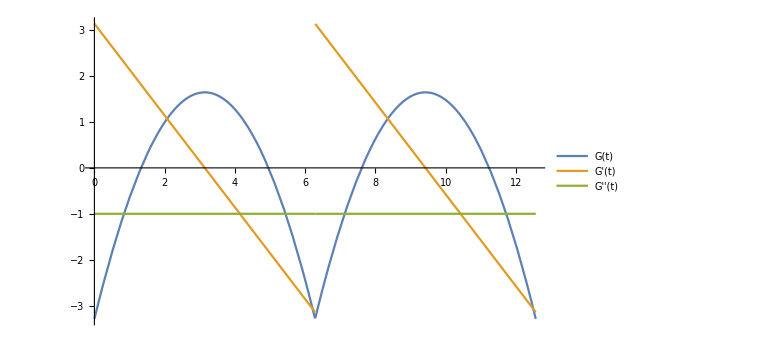

```mathematica
Plot[{G[t],G'[t],G''[t]},{t,0,4π},AxesOrigin->{0,0},PlotLegends->"Expressions",ImageSize->Large]
```